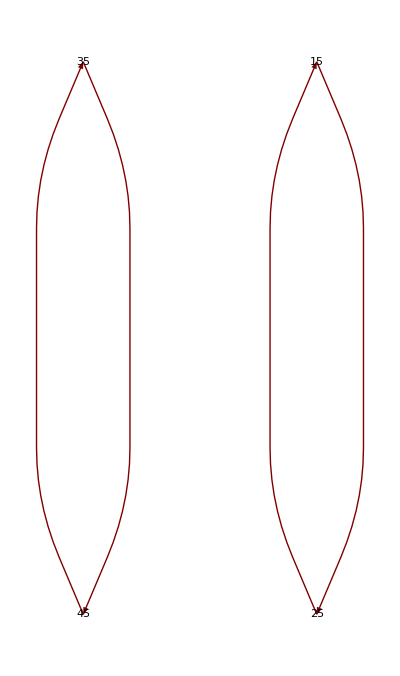

```mathematica
TreePlot[T26,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
CT26=Cycles[{{35,45},{15,25}}];
CT25=Cycles[{{35,45},{55,65}}];
CT24=Cycles[{{15,35,25,45},{26,28},{38,68}}];
CT23=Cycles[{{28,38},{26,68}}];
CT22=Cycles[{{28,68,58},{24,38,26}}];
CT21=Cycles[{{24,58},{26,68},{28,38},{22,48}}];
CT20=Cycles[{{24,26},{28,48},{58,68},{22,38}}];
CT19=Cycles[{{28,58,48,68},{22,26,38,24},{29,37},{57,67},{27,39}}];
CT18=Cycles[{{27,37,57},{38,68,58},{29,39,67},{24,28,26}}];
CT17=Cycles[{{22,24,38,48,58,28},{27,37,57},{29,39,67},{26,68}}];
CT16=Cycles[{{27,39,37,29,57,67},{24,26,48,38},{22,28,58,68},{23,69,49}}];
CT15=Cycles[{{23,57,49,27,69,37},{26,38,68,28},{29,39,67},{24,58}}];
CT14=Cycles[{{23,27,69,57,49,37},{24,38,58,28},{29,67,39},{26,68}}];
CT13=Cycles[{{27,67,37,39,57,29},{24,28,68,48},{22,58,38,26},{23,69,49}}];
CT12=Cycles[{{27,29,37,67,57,39},{24,28,58,38},{21,47,59},{22,48}}];
CT11=Cycles[{{22,24,26},{27,57,37},{23,69,49},{29,67,39},{48,58,68},{21,59,47}}];
CT10=Cycles[{{23,29,49,67,69,39},{21,27,47,57,59,37},{26,48,58},{22,24,68}}];
CT9=Cycles[{{24,28,26,46},{37,67,49,59},{38,68,66,58},{39,69,47,57},{21,27,29,23}}];
CT8=Cycles[{{48,66,56},{22,46,44}}];
CT7=Cycles[{{36,46,68},{26,64,66}}];
CT6=Cycles[{{38,54,64},{34,36,28}}];
CT5=Cycles[{{23,27,69,57,49,37},{21,39,59,29,47,67},{22,26,24},{48,68,58}}];
CT4=Cycles[{{22,58,68},{24,26,48}}];
CT3=Cycles[{{21,27,29,23},{24,32,26,38},{37,67,49,59},{39,69,47,57},{18,68,28,58}}];
CT2=Cycles[{{21,67,61,23},{22,24,64,26},{29,33,69,47},{36,68,48,58},{19,49,59,39}}];
CT1=Cycles[{{21,27,29,23},{22,68,28,62},{37,67,49,59},{39,69,47,57},{16,48,26,38}}];
CS8=Cycles[{{16,68,24,52},{15,65,25,55},{14,62,26,58}}];
CS7=Cycles[{{32,36,38,34},{17,61,29,57},{19,67,27,51},{18,64,28,54},{31,33,39,37}}];
CS6=Cycles[{{62,64,68,66},{13,33,29,49},{19,39,23,43},{16,36,26,46},{61,67,69,63}}];
CS5=Cycles[{{18,38,22,42},{15,35,25,45},{12,32,28,48}}];
CS3=Cycles[{{21,27,29,23},{24,28,26,22},{37,67,49,59},{39,69,47,57},{38,68,48,58}}];
CS2=Cycles[{{35,65,45,55},{36,66,44,54},{34,64,46,56}}];
CS9=Cycles[{{42,46,48,44},{11,63,23,59},{13,69,21,53},{12,66,22,56},{41,43,49,47}}];
CS4=Cycles[{{52,54,58,56},{11,31,27,47},{17,37,21,41},{14,34,24,44},{51,57,59,53}}];
CS1=Cycles[{{12,14,18,16},{31,61,43,53},{33,63,41,51},{32,62,42,52},{11,17,19,13}}];
```

```mathematica
CS1,CS2,CS3,CS4,CS5,CS6,CS7,CS8,CS9
CS2,CS3,CS5,CS6,CS7,CS8
CS2,CS3,CS6,CS7,CS8
CS2,CS3,CS7,CS8
CS2,CS3,CS7,CT1
CS2,CS3,CS7
CS2,CS3,CT2,CT3
CS2,CS3,CT2,CT4
CS2,CS3,CT4,CT5,CT6
CS3,CT4,CT5,CT7,CT8
CS3,CT4,CT5,CT8
CS3,CT4,CT5,CT9
CS3,CT4,CT5,CT10,CT11,CT12
CT4,CT13,CT14,CT15,CT16
CT4,CT17,CT18,CT19
CT4,CT20,CT21
CT22,CT23
CT23,CT24
CT25,CT26
CT25
```

```mathematica
group=PermutationGroup[{CT22,CT23}]
```

PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}]

```mathematica
GroupStabilizerChain[group,GroupActionBase->{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48,24,58,26,68}]
```

{{}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48}→PermutationGroup[{Cycles[{{24,38,26},{28,68,58}}],Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48,24}→PermutationGroup[{Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48,24,58}→PermutationGroup[{Cycles[{{26,68},{28,38}}]}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48,24,58,26}→PermutationGroup[{}],{11,41,53,12,42,13,63,43,14,52,15,25,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,22,48,24,58,26,68}→PermutationGroup[{}]}

```mathematica
PermutationGroup[{Cycles[{{22,58,68},{24,26,48}}],Cycles[{{23,67,57},{24,28,26},{27,49,39},{29,37,69},{38,68,58}}],Cycles[{{24,58},{26,38,68,28},{27,39},{29,37},{57,67}}],Cycles[{{24,68,58,26},{27,39},{28,38},{29,37},{57,67}}],Cycles[{{26,28},{27,29},{37,67},{38,68},{39,57}}],Cycles[{{27,57,37},{29,67,39}}],Cycles[{{26,68},{27,57,37},{28,38},{29,67,39}}]}]
```

```mathematica
group2=PermutationGroup[{CT23,CT24}]
```

PermutationGroup[{Cycles[{{26,68},{28,38}}],Cycles[{{15,35,25,45},{26,28},{38,68}}]}]

```mathematica
GroupOrbits[group2,{21,23,27,29}]
GroupOrbits[group2,{22,24,26}]
GroupOrbits[group2,{11,41,53,12,42,13,63,43,14,52,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48}]
```

{{21},{23},{27},{29}}

{{22},{24},{26,28,38,68}}

{{11},{12},{13},{14},{16},{17},{18},{19},{21},{22},{23},{27},{29},{31},{32},{33},{34},{36},{37},{39},{41},{42},{43},{44},{46},{47},{48},{49},{51},{52},{53},{54},{56},{57},{59},{61},{62},{63},{64},{66},{69}}